```mathematica
1+1
```

## Initialization

```mathematica
BlackScholesCall[s_,k_,σ_,r_,d_,t_]=1/2 Exp[-d t]s (Erf[((Sqrt[t] σ)/2+((r-d) t+Log[s/k])/(Sqrt[t] σ))/Sqrt[2]]+1)-1/2 Exp[-r t]  k (Erf[(((r-d) t+Log[s/k])/(Sqrt[t] σ)-(Sqrt[t] σ)/2)/Sqrt[2]]+1) ;
BlackScholesGamma[s_,k_,σ_,r_,d_,t_]=D[BlackScholesCall[s,k,σ,r,d,t], {s,2}]//FullSimplify ;
sT[s_,σ_,r_,d_,t_, random_]:=s Exp[(r-d-1/2 σ^2) t] Exp[σ Sqrt[t] random]
```

```mathematica
sm[x_,ϵ_]=2 ϵ PDF[NormalDistribution[0, Sqrt[2 ϵ]],x] + x CDF[NormalDistribution[0, Sqrt[2 ϵ]],x] ;
dd[x_,ϵ_]=PDF[NormalDistribution[0, Sqrt[2 ϵ]],x] ;
```

## Black-Scholes

```mathematica
TableForm[{BlackScholesCall[50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,1,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,1,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,1,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,0,1,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[0,0,0,0,0,1][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[2,0,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,1,0,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,1,0,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,1,0,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,1,0][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75],
Derivative[1,0,0,0,0,1][BlackScholesCall][50.0, 49.2,0.45, 0.05, 0.0, 0.75]
}, TableHeadings->{{"value", "d_s0","d_strike","d_vol", "d_ir","d_yield","d_bigT", "d_s0_s0", "d_s0_strike", "d_s0_vol","d_s0_ir","d_s0_yield","d_s0_bigT"}}]
```

value | 8.89865
d_s0 | 0.630232
d_strike | -0.459613
d_vol | 16.3459
d_ir | 16.9597
d_yield | -23.6337
d_bigT | 6.03441
d_s0_s0 | 0.0193729
d_s0_strike | -0.0196879
d_s0_vol | 0.0480192
d_s0_ir | 0.726483
d_s0_yield | -1.19916
d_s0_bigT | 0.062838

```mathematica
BlackScholesCall[ad[50.0, <|"s0"->1|>], ad[49.2,<|"strike"->1|>],ad[0.45,<|"vol"->1|>], ad[0.05,<|"ir"->1|>], ad[0.0, <|"yield"->1|>],ad[0.75, <|"bigT"->1|>]]
```

ad[8.89865,<|vol→16.3459,bigT→6.03441,strike→-0.459613,s0→0.630232,yield→-23.6337,ir→16.9597|>]

```mathematica
Derivative[1,0,0,0,0,0][BlackScholesCall][ad[50.0, <|"s0"->1|>], ad[49.2,<|"strike"->1|>],ad[0.45,<|"vol"->1|>], ad[0.05,<|"ir"->1|>], ad[0.0, <|"yield"->1|>],ad[0.75, <|"bigT"->1|>]]
```

ad[0.630232,<|s0→0.0193729,ir→0.726483,bigT→0.062838,vol→0.0480192,strike→-0.0196879,yield→-1.19916|>]

```mathematica
Derivative[2,0,0,0,0,0][BlackScholesCall][ad[50.0, <|"s0"->1|>], ad[49.2,<|"strike"->1|>],ad[0.45,<|"vol"->1|>], ad[0.05,<|"ir"->1|>], ad[0.0, <|"yield"->1|>],ad[0.75, <|"bigT"->1|>]]
```

ad[0.0193729,<|s0→-0.000718004,strike→0.000335921,yield→-0.00213419,ir→-0.0123955,bigT→-0.0139874,vol→-0.0438702|>]

```mathematica
sims=Module[{s0=50.0, strike=49.2, vol=0.45, ir=0.05, yield=0.0,bigT=0.75, nSims=10^3, rvs,paths, payoff, delta},
SeedRandom[123];
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
(* PV *)
{Mean[sims[[1]]], StandardDeviation[sims[[1]]] / Sqrt[Length[sims[[1]]]]}
```

{8.31979,0.474683}

```mathematica
(* Delta *)
{Mean[sims[[2]]], StandardDeviation[sims[[2]]] / Sqrt[Length[sims[[2]]]]}
```

{0.610494,0.021932}

```mathematica
sims=Module[{s0=ad[50.0, <|"s0"->1|>], strike=ad[49.2,<|"strike"->1|>], vol=ad[0.45,<|"vol"->1|>], ir=ad[0.05,<|"ir"->1|>], yield=ad[0.0, <|"yield"->1|>],bigT=ad[0.75, <|"bigT"->1|>], nSims=10^3, rvs,paths, payoff, delta},
SeedRandom[123];
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
(* PV *)
recursiveStatistics[sims[[1]]]
```

{ad[8.31979,<|strike→-0.451322,vol→14.9839,bigT→5.60543,yield→-22.8935,ir→16.6537,s0→0.610494|>],ad[0.474446,<|strike→-0.00897592,vol→1.2659,bigT→0.401852,yield→-0.687048,ir→0.331214,s0→0.0183213|>]}

```mathematica
(* Delta *)
recursiveStatistics[sims[[2]]]
```

{ad[0.610494,<|strike→-0.0149573,vol→0.0886069,bigT→0.063398,yield→-1.01011,ir→0.552239,s0→0.0147264|>],ad[0.021921,<|strike→0.0000310073,vol→0.0183197,bigT→0.00542027,yield→-0.0153061,ir→-0.00113463,s0→-0.0000302569|>]}

```mathematica
1-0.018830573493830043/0.019372891236998663
```

```mathematica
1-8.684181416829889/8.898647185376067
```

```mathematica
sims=Module[{s0=ad[50.0, <|s0->1|>], strike=ad[49.2,<|strike->1|>], vol=ad[0.45,<|vol->1|>], ir=ad[0.05,<|ir->1|>], yield=ad[0.0, <|yield->1|>],bigT=ad[0.75, <|bigT->1|>], nSims=10^4, nBuckets=10, rvs,paths, payoff, delta},
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff[p_]:=Exp[-ir bigT]sm[p-strike, 0.005];
delta[p_]:=Exp[-ir bigT] 1/2 Erfc[-((p-strike)/(2 Sqrt[0.005]))] p/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff[paths], delta[paths], payoff[#] & /@ Partition[paths, nSims/nBuckets], delta[#] & /@ Partition[paths, nSims/nBuckets]}
];
```

```mathematica
recursiveStatistics[sims[[1]]]
```

```mathematica
recursiveStatistics[sims[[2]]]
```

```mathematica
recursiveStatistics[recursiveStatistics[#] & /@ sims[[3]]]
```

```mathematica
recursiveStatistics[recursiveStatistics[#] & /@ sims[[4]]]
```

```mathematica
sims=Module[{s0=ad[50.0, <|s0->1|>], strike=ad[49.2,<|strike->1|>], vol=ad[0.45,<|vol->1|>], ir=ad[0.05,<|ir->1|>], yield=ad[0.0, <|yield->1|>],bigT=ad[0.75, <|bigT->1|>], nSims=10^4, rvs,paths, payoff, delta},
rvs=RandomVariate[NormalDistribution[0,1], {nSims}];
paths=sT[s0, vol, ir, yield, bigT, rvs];
payoff=Exp[-ir bigT]sm[paths-strike, 0.005];
delta=Exp[-ir bigT] 1/2 Erfc[-((paths-strike)/(2 Sqrt[0.005]))] paths/s0;
(*{Mean[payoff], StandardDeviation[payoff] / Sqrt[nSims]}*)
{payoff, delta}
];
```

```mathematica
Remove[pv, delta, valuation]
pv[s_,k_,σ_,r_,d_,t_,  rvs_]:=Exp[-r t] sm[sT[s, σ, r, d, t, rvs]-k, 0.005]
delta[s_,k_,σ_,r_,d_,t_,  rvs_]:=Derivative[1, 0,0,0,0,0,0][pv][s,k,σ,r,d,t,  rvs]
valuation[s_,k_,σ_,r_,d_,t_,  rvs_]:={pv[s,k,σ,r,d,t,  rvs], delta[s,k,σ,r,d,t,  rvs]}
```

```mathematica
rvs= RandomVariate[NormalDistribution[0,1], {2}];
```

```mathematica
pv[50.0, 49.2,0.45,0.05,0.0,0.75, rvs]
```

```mathematica
pv[ad[50.0, <|s0->1|>],  ad[49.2,<|strike->0|>], ad[0.45,<|vol->1|>], ad[0.05,<|ir->1|>], ad[0.0, <|yield->1|>],ad[0.75, <|bigT->1|>], rvs]
```

```mathematica
recursiveStatistics /@ valuation[ad[50.0, <|s0->1|>],  ad[49.2,<|strike->1|>], ad[0.45,<|vol->1|>], ad[0.05,<|ir->1|>], ad[0.0, <|yield->1|>],ad[0.75, <|bigT->1|>], rvs]
```

```mathematica
1-0.6358062897035217/0.6302323426665506
```

```mathematica
1-0.021137877396396637/0.019372891236998663
```

## Work

### Examples

```mathematica
ad[1.23, 5.67]
```

```mathematica
ad[x1, <|x1->y1|>]
```

```mathematica
ad[x1, <|x1->y1|>]+3
```

```mathematica
-2ad[x1, <|x1->y1|>]
```

```mathematica
ad[x1, <|x1->y1|>]+ad[x2, <|x2->y2|>]
```

```mathematica
ad[expr1, <|x1->y1, x3->y3|>]+ad[expr2, <|x2->y2, x4->y4|>]
```

ad[expr1+expr2,<|x1→y1,x3→y3,x2→y2,x4→y4|>]

```mathematica
ad[expr1, <|x1->y1, x3->y3|>] ad[expr2, <|x2->y2, x4->y4|>]
```

```mathematica
ad[x1, <|x1->y1|>]^(-2)
```

```mathematica
ad[Tan[x1], <|x1-> y1|>]+ad[x2, <|x2->y2|>]
```

```mathematica
ad[x1, <|x1->y1|>]+ad[x2, <|x2->y2|>]
```

```mathematica
ad[x1, <|x1->y1|>]+3ad[x2, <|x2->y2|>]
```

```mathematica
ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]
```

```mathematica
Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

ad[Sin[x1 x2],<|x1→x2 y1 Cos[x1 x2],x2→x1 y2 Cos[x1 x2]|>]

```mathematica
ad[x3, <|x3->y3|>] Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

```mathematica
Exp[ad[x3, <|x3->y3|>] Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
Exp[ad[x2, <|x2->y2|>] Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
Exp[ad[x3, <|x3->y3|>] Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]]]
```

```mathematica
D[Exp[x3 Sin[x1 x2]], {{x1, x2, x3}}]
```

```mathematica
Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]] Cos[ad[x3, <|x3->y3|>] ad[x4, <|x4->y4|>]^3] (Log[Tan[ad[x5, <|x5-> y5|>]/ad[x6, <|x6->y6|>]]])^(-2)
```

```mathematica
Trace[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]]//MatrixForm
```

```mathematica
With[{local=Exp[ad[x3, <|x3->y3|>] Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]]]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=D[Exp[x3 Sin[x1 x2]], {{x1, x2, x3}}]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=Tan[Exp[ad[x3, <|x3->y3|>] Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]]]+Log[ad[x3, <|x3->y3|>] ad[x1, <|x1->y1|>]]]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
With[{local=D[Tan[Exp[x3] Sin[x1 x2]+Log[x3 x1]], {{x1, x2, x3}}]//Trace}, 
TableForm[local, TableHeadings->{Range[Length[local]], None}]]
```

```mathematica
Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]
```

```mathematica
traceView2[ D[Sin[x1+x2],{{x1,x2}}]]
```

```mathematica
D[Sin[x1+x2],{{x1,x2}}]//Grap
```

```mathematica
traceView2[Sin[ad[x1 x2,<|x1->x2 y1,x2->x1 y2|>]]]
```

```mathematica
traceView2[D[Sin[x1 x2], {{x1, x2}}]]
```

```mathematica
traceView2[Tan[Exp[ad[x3, <|x3->y3|>] Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]]]+Log[ad[x3, <|x3->y3|>] ad[x1, <|x1->y1|>]]]]
```

```mathematica
traceView2[D[Tan[Exp[x3] Sin[x1 x2]+Log[x3 x1]], {{x1, x2, x3}}]]
```

```mathematica
traceView2[Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]] Cos[ad[x3, <|x3->y3|>] ad[x4, <|x4->y4|>]^3] (Log[Tan[ad[x5, <|x5-> y5|>]/ad[x6, <|x6->y6|>]]])^(-2)]
```

```mathematica
traceView2[D[Sin[x1 x2] Cos[x3 x4^3] (Log[Tan[x5/x6]])^(-2),{{x1,x2,x3,x4,x5,x6}}]]
```

```mathematica
LeafCount[ad[x1, <|x1->y1|>] + ad[x1, <|x1->y1|>]]
```

```mathematica
LeafCount[D[x1+x2,{{x1, x2}}]]
```

```mathematica
LeafCount[Sin[ad[x1, <|x1->y1|>] + ad[x1, <|x1->y1|>]]]
```

```mathematica
LeafCount[D[Sin[x1+x2],{{x1, x2}}]]
```

```mathematica
LeafCount[Sin[ad[x1, <|x1->y1|>] ad[x2, <|x2->y2|>]] Cos[ad[x3, <|x3->y3|>] ad[x4, <|x4->y4|>]^3] (Log[Tan[ad[x5, <|x5-> y5|>]/ad[x6, <|x6->y6|>]]])^(-2)]
```

```mathematica
LeafCount[D[Sin[x1 x2] Cos[x3 x4^3] (Log[Tan[x5/x6]])^(-2),{{x1,x2,x3,x4,x5,x6}}]]
```

```mathematica
Mean[{ad[x1, <|x1-> y1|>], ad[x2, <|x2-> y2|>], ad[x3, <|x3-> y3|>]}]
```

```mathematica
StandardDeviation[{ad[x1, <|x1-> y1|>], ad[x2, <|x2-> y2|>], ad[x3, <|x3-> y3|>]}] /. Conjugate[z_] -> z
```

```mathematica
m={{ad[x1, <|x1-> y1|>], ad[x2, <|x2-> y2|>]},{ad[x3, <|x3-> y3|>], ad[x4, <|x4-> y4|>]}};
```

```mathematica
m//MatrixForm
```

```mathematica
Tr[m]
```

```mathematica
Det[m]
```

```mathematica
Inverse[m] //MatrixForm
```

```mathematica
ad[1.23, <|x1->y1|>]+ad[4.56, <|x2-> y2|>]
```

```mathematica
ad[1.23, <|x1->y1|>] ad[4.56, <|x2-> y2|>]
```

```mathematica
Log[Sin[ad[1.23, <|x1->y1|>]]]
```

```mathematica
Derivative[1][Log[Sin[#]]&][1.23]
```

```mathematica
ad[1.23, <|x1->y1, x3->y3|>]+ad[4.56, <|x2-> y2|>]
```

```mathematica
ad[1.23, <|x1->y1, x3->y3|>] ad[4.56, <|x2-> y2|>]
```

```mathematica
counter=0;
out=ad[x,<|x->y|>];
While[
counter<4, 
out=Sin[out];
counter++
]
```

```mathematica
out
```

```mathematica
Solve[ad[a,<|a->ya|>] x^2+ad[b,<|b->yb|>] x+ad[c,<|c->yc|>]==0,x]
```

```mathematica
psi=PseudoInverse[{{ad[1, <|x1->y1|>], ad[2, <|x2->y2|>], ad[3, <|x3->y3|>]}, {ad[4, <|x4->y4|>], ad[5, <|x5->y5|>], ad[6, <|x6->y6|>]}, {ad[7, <|x7->y7|>], ad[8, <|x8->y8|>], ad[9, <|x9->y9|>]}}];
```

```mathematica
Conjugate[ad[5,<|x5->y5|>]]
```

```mathematica
Conjugate[ad[5,<|x5->y5|>]] /. toValue[z_]
```

```mathematica
ad[5,<|x5->y5|>]// toValue
```

```mathematica
Solve[ad[a,<|a->ya|>] x^2+ad[b,<|b->yb|>] x+ad[c,<|c->yc|>]==0,x]//toValue
```

```mathematica
ad[x1, <|x1->y1|>]^ad[x2, <|x2->y2|>]
```

```mathematica
ad[x1, <|x1->y1|>]^ad[x2, <|x2->y2|>]
```

```mathematica
E^ad[x,<|x->y|>]
```

```mathematica
Exp[ad[x,<|x->y|>]]
```

```mathematica
ad[x1,<|x1->y1|>] ad[x2,<|x2->y2|>]
```

```mathematica
D[x1 x2,{{x1, x2}}]
```

```mathematica
ad[1.23,<|x1->y1|>] ad[4.56,<|x2->y2|>]
```

```mathematica
propagatead[ff, {expr1, expr2}, {<|x1->y1, x2->y2|>, <|x3->y3|>}]
```

```mathematica
propagatead[ff, {expr1, expr2}, {<|x1->y1, x2->y2|>, <|x2->y3|>}]
```

```mathematica
KeyUnion[{<|x1->y1, x2->y2|>, <|x2->y3|>}]
```

```mathematica
Merge[{<|a->1,b->2|>,<|b->4,c->5|>},Total]
```

```mathematica
Merge[<|a->1,b->2|>]
```

```mathematica
Sin[ad[x+I y, <|x1->y1, x2->y2|>]]
```

### Graphs

\[Theta]={Subscript[\[Theta], 1], Subscript[\[Theta], 2]}
nM= 3 - time steps
nMC=4  - simulations

```mathematica
nE=3;
nMC=2;
```

```mathematica
x0=Table[Subscript[x, 0,m], {m, nE}]
```

{x_(0,1),x_(0,2),x_(0,3)}

```mathematica
spot=Table[Subscript[x, m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
spot
```

{{x_1^1,x_2^1,x_3^1},{x_1^2,x_2^2,x_3^2}}

```mathematica
vol=Table[Subscript[σ, n], {n, ToString /@Range[nE]}]
```

{σ_1,σ_2,σ_3}

```mathematica
cashE=Table[Subscript["E", m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
continuationH=Table[Subscript["H", m]^n,{n, ToString /@Range[nMC]}, {m, ToString /@Range[nE]}];
```

```mathematica
beta=Table[Subscript[β, n], {n, ToString /@Range[nE-1]}];
```

```mathematica
(*graphSpotProcess=Flatten[Thread[#[[1]]-> #[[2]]]& /@ Partition[Join[{x0}, Transpose[spot]], 2, 1], 1];*)
```

```mathematica
values=Table[Subscript[V, n]^m, {n, ToString /@Range[nE]}, {m,  ToString /@Range[nMC]}];
```

```mathematica
graphSpotProcess=Flatten[Thread[#[[1]]->#[[2;;]]] & /@ Transpose[Join[{x0}, spot]]];
```

```mathematica
graphVol=Flatten[(Thread@@{vol->  #}) & /@ spot, 1];
```

```mathematica
graphcashE=Flatten[MapThread[Thread[#1-> #2] &, {spot, cashE}],1];
```

```mathematica
(*graphcontinuationH=Flatten[MapThread[Thread[#1->#2] &, {spot, continuationH}],1];*)
```

```mathematica
graphcontinuationH=Join[Flatten[MapThread[Thread[#1->#2] &, {Transpose[spot][[1;;-2]], Transpose[continuationH][[1;;-2]]}],1],Flatten[MapThread[Thread[#1->#2]&, {beta, Transpose[continuationH][[1;;-2]]}], 1]];
```

```mathematica
graphBeta=Join[Flatten[MapThread[Thread[#1->#2]&,{Transpose[spot][[1;;-2]], beta}], 1], Flatten[MapThread[Thread[#1->#2] &, {values[[2;;]], beta}]]]
```

{x_1^1→β_1,x_1^2→β_1,x_2^1→β_2,x_2^2→β_2,V_2^1→β_1,V_2^2→β_1,V_3^1→β_2,V_3^2→β_2}

```mathematica
graphvalues=Join[Flatten[MapThread[Thread[#1->#2]&, {Transpose[cashE], values}], 1],Flatten[MapThread[Thread[#1->#2]&, {Transpose[continuationH][[1;;-2]], values[[1;;-2]]}], 1] ,Flatten[Thread[#[[1]]-> #[[2]]] & /@ Partition[Reverse[values], 2, 1], 1] ];
```

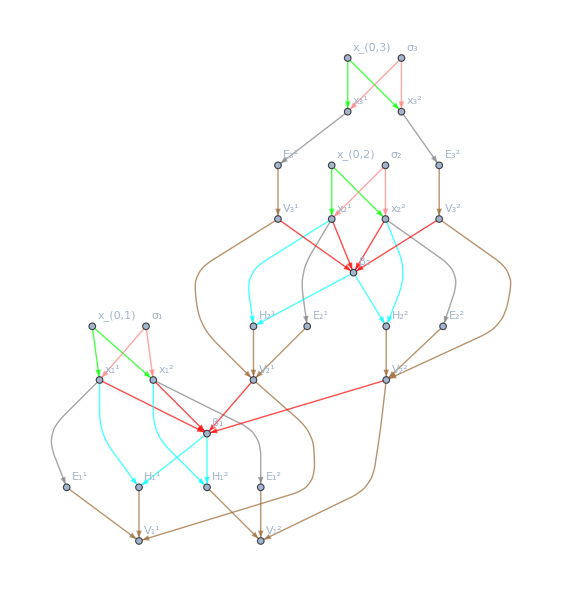

```mathematica
mess=Graph[Join[graphSpotProcess, graphVol, graphcashE, graphcontinuationH, graphBeta, graphvalues], VertexLabels-> "Name", EdgeStyle-> Join[Thread[graphSpotProcess->  Green], Thread[graphVol->  Pink],Thread[graphcashE->  Gray], Thread[graphcontinuationH->  Cyan], Thread[graphBeta-> Red], Thread[graphvalues-> Brown]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"UserGuide", "graph.pdf"}], mess]
```

C:\Users\fsiano\work\dev\workspace\AD\UserGuide\graph.pdf

## Junk

```mathematica
assocToTable[a_Association]:=TableForm[Values[a], TableHeadings->{Keys[a]}]
```

### Bermudan

#### Inputs

```mathematica
elapsedStart=Date[];
SeedRandom[123];
nE=30;
nMC=10^1;
nB=5;
rvs=RandomVariate[NormalDistribution[0, 1] ,{nMC, nE}];
forward=23.0+10 Sin[2 π Range[nE]/60];
(*forward=ad[#, <|Unique["fc"]->1|>] & /@ forward;*)
forward=MapThread[ad[#1, <|#2->1|>]&,{forward, "fc"<>ToString[#] & /@ Range[nE]}];
sigma = 0.45;
(*tv=Sqrt[Range[nE]/365.242 ad[0.45, <|Unique["vol"]->1|>]^2];*)
(*tv=Sqrt[Range[nE]/365.242]  (ad[sigma, <|Unique["vol"]->1|>] & /@ Range[nE]);*)
tv=Sqrt[Range[nE]/365.242] MapThread[ad[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}]
spot=simulationSpot[forward, tv, rvs ];

irt = 0.0245 Range[1/ 365.242, nE/365.242, 1/365.242] & /@ Range[nMC];
numeraire=Exp[irt];

(*strike=RandomReal[MinMax[Flatten[spot[[All, All, 1]]]]];*)
strike=Mean[Flatten[spot[[All, All, 1]]]];

exerciseValue=Map[payoffBermudean[#, strike] &,spot, {2}];

basisFunctions = Function[x,Evaluate@Table[LaguerreL[n,x], {n,nB}]];

phi = basisFunctions[spot];
elapsedEnd=Date[];
```

{ad[0.0235463,<|vol1→0.052325|>],ad[0.0332995,<|vol2→0.0739988|>],ad[0.0407833,<|vol3→0.0906296|>],ad[0.0470925,<|vol4→0.10465|>],ad[0.0526511,<|vol5→0.117002|>],ad[0.0576764,<|vol6→0.12817|>],ad[0.0622976,<|vol7→0.138439|>],ad[0.0665989,<|vol8→0.147998|>],ad[0.0706388,<|vol9→0.156975|>],ad[0.0744599,<|vol10→0.165466|>],ad[0.0780941,<|vol11→0.173543|>],ad[0.0815667,<|vol12→0.181259|>],ad[0.0848973,<|vol13→0.188661|>],ad[0.0881021,<|vol14→0.195782|>],ad[0.0911943,<|vol15→0.202654|>],ad[0.0941851,<|vol16→0.2093|>],ad[0.0970838,<|vol17→0.215742|>],ad[0.0998984,<|vol18→0.221996|>],ad[0.102636,<|vol19→0.22808|>],ad[0.105302,<|vol20→0.234005|>],ad[0.107903,<|vol21→0.239783|>],ad[0.110442,<|vol22→0.245426|>],ad[0.112924,<|vol23→0.250942|>],ad[0.115353,<|vol24→0.256339|>],ad[0.117731,<|vol25→0.261625|>],ad[0.120063,<|vol26→0.266806|>],ad[0.12235,<|vol27→0.271889|>],ad[0.124595,<|vol28→0.276878|>],ad[0.126801,<|vol29→0.281779|>],ad[0.128968,<|vol30→0.286596|>]}

```mathematica
DateDifference[elapsedStart, elapsedEnd, "Second"]
```

178.051 s

```mathematica
forward
```

{ad[24.0453,<|fc1→1|>],ad[25.0791,<|fc2→1|>],ad[26.0902,<|fc3→1|>],ad[27.0674,<|fc4→1|>],ad[28.,<|fc5→1|>],ad[28.8779,<|fc6→1|>],ad[29.6913,<|fc7→1|>],ad[30.4314,<|fc8→1|>],ad[31.0902,<|fc9→1|>],ad[31.6603,<|fc10→1|>],ad[32.1355,<|fc11→1|>],ad[32.5106,<|fc12→1|>],ad[32.7815,<|fc13→1|>],ad[32.9452,<|fc14→1|>],ad[33.,<|fc15→1|>],ad[32.9452,<|fc16→1|>],ad[32.7815,<|fc17→1|>],ad[32.5106,<|fc18→1|>],ad[32.1355,<|fc19→1|>],ad[31.6603,<|fc20→1|>],ad[31.0902,<|fc21→1|>],ad[30.4314,<|fc22→1|>],ad[29.6913,<|fc23→1|>],ad[28.8779,<|fc24→1|>],ad[28.,<|fc25→1|>],ad[27.0674,<|fc26→1|>],ad[26.0902,<|fc27→1|>],ad[25.0791,<|fc28→1|>],ad[24.0453,<|fc29→1|>],ad[23.,<|fc30→1|>]}

```mathematica
tv
```

{ad[0.0235463,<|vol1→0.052325|>],ad[0.0332995,<|vol2→0.0739988|>],ad[0.0407833,<|vol3→0.0906296|>],ad[0.0470925,<|vol4→0.10465|>],ad[0.0526511,<|vol5→0.117002|>],ad[0.0576764,<|vol6→0.12817|>],ad[0.0622976,<|vol7→0.138439|>],ad[0.0665989,<|vol8→0.147998|>],ad[0.0706388,<|vol9→0.156975|>],ad[0.0744599,<|vol10→0.165466|>],ad[0.0780941,<|vol11→0.173543|>],ad[0.0815667,<|vol12→0.181259|>],ad[0.0848973,<|vol13→0.188661|>],ad[0.0881021,<|vol14→0.195782|>],ad[0.0911943,<|vol15→0.202654|>],ad[0.0941851,<|vol16→0.2093|>],ad[0.0970838,<|vol17→0.215742|>],ad[0.0998984,<|vol18→0.221996|>],ad[0.102636,<|vol19→0.22808|>],ad[0.105302,<|vol20→0.234005|>],ad[0.107903,<|vol21→0.239783|>],ad[0.110442,<|vol22→0.245426|>],ad[0.112924,<|vol23→0.250942|>],ad[0.115353,<|vol24→0.256339|>],ad[0.117731,<|vol25→0.261625|>],ad[0.120063,<|vol26→0.266806|>],ad[0.12235,<|vol27→0.271889|>],ad[0.124595,<|vol28→0.276878|>],ad[0.126801,<|vol29→0.281779|>],ad[0.128968,<|vol30→0.286596|>]}

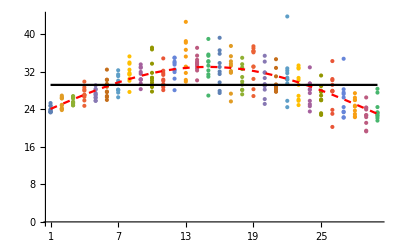

```mathematica
Which[NumericQ[forward[[1]]], 
Show[ListPlot[spot, Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle->Red], ListPlot[strike & /@ forward, PlotStyle->Black]]
, Head[forward[[1]]]==ad, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[spot[[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"]
```

```mathematica
(*bigA=Outer[Total[#1 #2] &, basis, basis, 1,  1];*)
bigA=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,1;;-2]],{2,3,1}];
```

```mathematica
bigA //Dimensions
```

{1,5,5}

```mathematica
bigA = Inverse /@ bigA;
bigA // Dimensions
```

{1,5,5}

```mathematica
phi[[All, All, -2]][[All, All, 1]]
```

{{-23.7517,-23.2275,-22.1973,-22.0535,-23.1711,-22.0938,-23.8149,-23.2646,-23.8558,-23.9182},{257.821,246.03,223.663,220.625,244.779,221.473,259.261,246.855,260.193,261.621},{-1681.63,-1561.36,-1341.89,-1312.98,-1548.78,-1321.03,-1696.53,-1569.68,-1706.21,-1721.06},{7269.62,6540.06,5266.,5104.02,6464.98,5148.99,7361.46,6589.8,7421.29,7513.32},{-21556.5,-18668.6,-13879.1,-13295.5,-18377.2,-13456.9,-21927.,-18862.3,-22169.1,-22542.8}}

```mathematica
(*bigB=Total[numeraire[[All,-2]]/numeraire[[All, -1]] values basis[[#, All]]]  & /@ Range[nB]*)
bigB=With[{day=-2},
seqsum[numeraire[[All,day]]/numeraire[[All,day+1]] exerciseValue[[All,day+1]] #]&/@phi[[All,All,day]]
];
```

```mathematica
Dot[bigA[[-2+1]], bigB]
```

{ad[15.5515,<|vol5→14.662,fc3→-42.8713,vol6→17.092,fc4→17.4331|>],ad[-2.33612,<|vol5→-21.0401,fc3→3.2307,vol6→-2.56768,fc4→-2.61869|>],ad[-0.399804,<|vol5→0.215665,fc3→0.40438,vol6→-0.439417,fc4→-0.448175|>],ad[0.0613036,<|vol5→0.268729,fc3→-0.190475,vol6→0.0674757,fc4→0.0686324|>],ad[0.00508123,<|vol5→-0.210122,fc3→-0.00143009,vol6→0.00561843,fc4→0.00566554|>]}

```mathematica
beta=Dot[Inverse[bigA], bigB]
```

```mathematica
Dot[beta, # ] & /@  Transpose[basis]
```

```mathematica
Dot[Transpose[basis], beta]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-3]], Rationalize[bigB, 10^-3]],  basis[[All, -1]]]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-4]], Rationalize[bigB, 10^-4]],  basis[[All, -1]]]
```

```mathematica
Dot[Dot[Inverse[Rationalize[bigA, 10^-6]], Rationalize[bigB, 10^-6]],  basis[[All, -1]]]
```

```mathematica
Function[x,Evaluate@Table[LaguerreL[n,x], {n, 5}]][spot] //Dimensions
```

```mathematica
AbsoluteTiming[1+1]
```

{3.84954×10^-6,2}

```mathematica
{elapsed, {bs, vs, hs}}=AbsoluteTiming[regressionCoefficient[Function[x,Evaluate@Table[LaguerreL[n,x], {n, nB}]],spot,numeraire,exerciseValue, exerciseValue[[All, -1]]]];
```

```mathematica
elapsed
```

368.81

```mathematica
vs //Dimensions
```

{30,10}

Reconcile day=-2

```mathematica
bigAm2=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-2;;-2]],{2,3,1}];
```

```mathematica
bigAm2=bigAm2[[1]];
```

```mathematica
bigAm2//Dimensions
```

{5,5}

```mathematica
valuesFinal=exerciseValue[[All,-2+1]];
bigBm2=seqsum[numeraire[[All,-2]]/numeraire[[All,-2+1]] valuesFinal #]&/@phi[[All,All,-2]];
```

```mathematica
bigBm2//Dimensions
```

{5}

```mathematica
betam2=Dot[Inverse[bigAm2], bigBm2];
```

```mathematica
betam2//Dimensions
```

{5}

```mathematica
hm2=Dot[betam2, phi[[All, All, -2]]];
```

```mathematica
hm2//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-2]],hm2,numeraire[[All,-2]]/numeraire[[All,-2+1]] valuesFinal}];
```

```mathematica
betam2[[5]]
```

ad[0.,<|vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol28→0.,fc28→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]

```mathematica
bs[[1]]
```

{ad[-2.33557×10^-31,<|vol29→-2.40168×10^-28,fc29→-1.88901×10^-29,vol30→-4.96874×10^-28,fc30→-4.85863×10^-29|>],ad[-8.21425×10^-32,<|vol29→-8.44736×10^-29,fc29→-6.63965×10^-30,vol30→-1.74751×10^-28,fc30→-1.70879×10^-29|>],ad[-1.76755×10^-32,<|vol29→-1.81816×10^-29,fc29→-1.42803×10^-30,vol30→-3.76031×10^-29,fc30→-3.67698×10^-30|>],ad[-2.5307×10^-33,<|vol29→-2.60306×10^-30,fc29→-2.04317×10^-31,vol30→-5.38387×10^-30,fc30→-5.26455×10^-31|>],ad[-1.99831×10^-34,<|vol29→-2.05341×10^-31,fc29→-1.61109×10^-32,vol30→-4.25123×10^-31,fc30→-4.15702×10^-32|>]}

Reconcile day=-3

```mathematica
bigAm3=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-3;;-3]],{2,3,1}];
```

```mathematica
bigAm3=bigAm3[[1]];
```

```mathematica
bigAm3//Dimensions
```

{5,5}

```mathematica
bigBm3=seqsum[numeraire[[All,-3]]/numeraire[[All,-3+1]] valuesFinal #]&/@phi[[All,All,-3]];
```

```mathematica
betam3=Dot[Inverse[bigAm3], bigBm3];
```

```mathematica
betam3//Dimensions
```

{5}

```mathematica
hm3=Dot[betam3, phi[[All, All, -3]]];
```

```mathematica
hm3//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-3]],hm3,numeraire[[All,-3]]/numeraire[[All,-3+1]] valuesFinal}];
```

```mathematica
betam3
```

{ad[-0.0725133,<|vol28→-0.1107,fc28→0.172193,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000214013,<|vol28→-0.108328,fc28→-0.00822423,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.00150946,<|vol28→-0.0206598,fc28→-0.00426732,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000288786,<|vol28→-0.0034727,fc28→-0.000133445,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[-0.000132183,<|vol28→-0.000642653,fc28→0.0000185117,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol27→0.,fc27→0.,vol30→0.,fc30→0.,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]}

```mathematica
bs[[2]]//TableForm
```

ad[-0.0673022,<|vol28→-0.102167,fc28→0.15846,vol29→2.9802×10^-29,fc29→2.35721×10^-30,vol30→6.31548×10^-29,fc30→6.17552×10^-30|>]
ad[-0.00012196,<|vol28→-0.0998054,fc28→-0.00764027,vol29→-2.4529×10^-32,fc29→-2.0178×10^-33,vol30→-5.66443×10^-32,fc30→-5.5389×10^-33|>]
ad[0.00139766,<|vol28→-0.0188,fc28→-0.00391961,vol29→-6.44663×10^-31,fc29→-5.10125×10^-32,vol30→-1.36747×10^-30,fc30→-1.33717×10^-31|>]
ad[-0.000266688,<|vol28→-0.00315763,fc28→-0.000118429,vol29→1.17865×10^-31,fc29→9.32196×10^-33,vol30→2.49732×10^-31,fc30→2.44198×10^-32|>]
ad[-0.000121284,<|vol28→-0.000595418,fc28→0.0000170308,vol29→5.46125×10^-32,fc29→4.32016×10^-33,vol30→1.15764×10^-31,fc30→1.13198×10^-32|>]

Reconcile day=-4

```mathematica
bigAm4=Function[x,Outer[seqsum[#1 #2]&,x,x,1,1]][#]&/@Transpose[phi[[All,All,-4;;-4]],{2,3,1}];
```

```mathematica
bigAm4=bigAm4[[1]];
```

```mathematica
bigAm4//Dimensions
```

{5,5}

```mathematica
bigBm4=seqsum[numeraire[[All,-4]]/numeraire[[All,-4+1]] valuesFinal #]&/@phi[[All,All,-4]];
```

```mathematica
betam4=Dot[Inverse[bigAm4], bigBm4];
```

```mathematica
betam4//Dimensions
```

{5}

```mathematica
hm4=Dot[betam4, phi[[All, All, -4]]];
```

```mathematica
hm4//Dimensions
```

{10}

```mathematica
valuesFinal=MapThread[vf[#1,#2,#3]&,{exerciseValue[[All,-4]],hm4,numeraire[[All,-4]]/numeraire[[All,-4+1]] valuesFinal}];
```

```mathematica
betam4
```

{ad[0.75866,<|vol27→-19.524,fc27→-0.0243209,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-2.35924,fc28→-0.162533,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.228361,<|vol27→-6.07928,fc27→-0.0246977,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.679241,fc28→-0.0308982,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.0406455,<|vol27→-1.08761,fc27→-0.00625999,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.113158,fc28→-0.000984351,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.00459035,<|vol27→-0.122854,fc27→-0.000889123,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.0118198,fc28→0.000471615,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>],ad[0.000265266,<|vol27→-0.00721955,fc27→-0.0000659425,vol29→0.,fc29→0.,vol1→0.,fc1→0.,vol4→0.,fc4→0.,vol7→0.,fc7→0.,vol15→0.,fc15→0.,vol18→0.,fc18→0.,vol19→0.,fc19→0.,vol20→0.,fc20→0.,vol21→0.,fc21→0.,vol22→0.,fc22→0.,vol23→0.,fc23→0.,vol24→0.,fc24→0.,vol26→0.,fc26→0.,vol30→0.,fc30→0.,vol28→-0.000632427,fc28→0.0000602494,vol25→0.,fc25→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol8→0.,fc8→0.,vol12→0.,fc12→0.,vol14→0.,fc14→0.,vol13→0.,fc13→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol6→0.,fc6→0.,vol5→0.,fc5→0.,vol2→0.,fc2→0.,vol3→0.,fc3→0.|>]}

```mathematica
bs[[3]]//TableForm
```

ad[0.772138,<|vol27→-19.7453,fc27→-0.0237078,vol29→-2.08235×10^-28,fc29→-1.652×10^-29,vol30→-4.44985×10^-28,fc30→-4.35124×10^-29,vol28→-0.936444,fc28→0.370289|>]
ad[0.232313,<|vol27→-6.15539,fc27→-0.0251066,vol29→-6.34001×10^-29,fc29→-5.02937×10^-30,vol30→-1.35449×10^-28,fc30→-1.32447×10^-29,vol28→-0.234683,fc28→0.138606|>]
ad[0.0413096,<|vol27→-1.10054,fc27→-0.0063674,vol29→-1.13888×10^-29,fc29→-9.03434×10^-31,vol30→-2.43295×10^-29,fc30→-2.37903×10^-30,vol28→-0.026694,fc28→0.0322653|>]
ad[0.00466019,<|vol27→-0.124175,fc27→-0.000902642,vol29→-1.29471×10^-30,fc29→-1.02706×10^-31,vol30→-2.76586×10^-30,fc30→-2.70456×10^-31,vol28→-0.000999309,fc28→0.00465487|>]
ad[0.000269048,<|vol27→-0.00729442,fc27→-0.0000669481,vol29→-7.50923×10^-32,fc29→-5.95699×10^-33,vol30→-1.60422×10^-31,fc30→-1.56867×10^-32,vol28→0.000051324,fc28→0.000326315|>]

```mathematica
bs//Dimensions
```

{29,5}

```mathematica
Values[<|"vol28"->-0.10216705428319983,"fc28"->0.15845966521033006,"vol29"->2.980201245957065*^-29,"fc29"->2.3572054152826975*^-30,"vol30"->6.315478266316725*^-29,"fc30"->6.1755180480215595*^-30|>]
```

{-0.102167,0.15846,2.9802×10^-29,2.35721×10^-30,6.31548×10^-29,6.17552×10^-30}

```mathematica
bs[[2]]/. ad[expr_, a_] -> ad[expr, assocToTable[a]] //TableForm
```

ad[-0.0673022,vol28 | -0.102167
fc28 | 0.15846
vol29 | 2.9802×10^-29
fc29 | 2.35721×10^-30
vol30 | 6.31548×10^-29
fc30 | 6.17552×10^-30]
ad[-0.00012196,vol28 | -0.0998054
fc28 | -0.00764027
vol29 | -2.4529×10^-32
fc29 | -2.0178×10^-33
vol30 | -5.66443×10^-32
fc30 | -5.5389×10^-33]
ad[0.00139766,vol28 | -0.0188
fc28 | -0.00391961
vol29 | -6.44663×10^-31
fc29 | -5.10125×10^-32
vol30 | -1.36747×10^-30
fc30 | -1.33717×10^-31]
ad[-0.000266688,vol28 | -0.00315763
fc28 | -0.000118429
vol29 | 1.17865×10^-31
fc29 | 9.32196×10^-33
vol30 | 2.49732×10^-31
fc30 | 2.44198×10^-32]
ad[-0.000121284,vol28 | -0.000595418
fc28 | 0.0000170308
vol29 | 5.46125×10^-32
fc29 | 4.32016×10^-33
vol30 | 1.15764×10^-31
fc30 | 1.13198×10^-32]

```mathematica
vs[[1]]
```

{ad[0.0282095,<|vol29→-2.01067×10^-29,fc29→-1.59364×10^-30,vol30→-4.27903×10^-29,fc30→-4.1842×10^-30|>],ad[0.0282095,<|vol29→-6.2161×10^-30,fc29→-4.89732×10^-31,vol30→-1.30759×10^-29,fc30→-1.27861×10^-30|>],ad[0.0282095,<|vol29→-3.35963×10^-30,fc29→-2.63123×10^-31,vol30→-6.99119×10^-30,fc30→-6.83626×10^-31|>],ad[9.78300931981276×10^-974,<|vol30→2.63323363780108×10^-970,fc30→9.81968558723149×10^-971|>],ad[0.0282095,<|vol29→-1.40024×10^-29,fc29→-1.10775×10^-30,vol30→-2.96798×10^-29,fc30→-2.9022×10^-30|>],ad[0.0282095,<|vol29→-1.95953×10^-29,fc29→-1.55166×10^-30,vol30→-4.16077×10^-29,fc30→-4.06857×10^-30|>],ad[0.0282095,<|vol29→-2.4412×10^-30,fc29→-1.90281×10^-31,vol30→-5.03588×10^-30,fc30→-4.92428×10^-31|>],ad[0.0282095,<|vol29→-1.58492×10^-29,fc29→-1.25435×10^-30,vol30→-3.36189×10^-29,fc30→-3.28738×10^-30|>],ad[0.0282095,<|vol29→-1.39244×10^-29,fc29→-1.10156×10^-30,vol30→-2.95134×10^-29,fc30→-2.88593×10^-30|>],ad[0.0282095,<|vol29→-2.03153×10^-29,fc29→-1.60994×10^-30,vol30→-4.32185×10^-29,fc30→-4.22608×10^-30|>]}

```mathematica
bs[[2]] /. ad[expr_, a_] -> ad[expr, assocToTable[a]] //TableForm
```

ad[-0.0673022,vol28 | -0.102167
fc28 | 0.15846
vol29 | 2.9802×10^-29
fc29 | 2.35721×10^-30
vol30 | 6.31548×10^-29
fc30 | 6.17552×10^-30]
ad[-0.00012196,vol28 | -0.0998054
fc28 | -0.00764027
vol29 | -2.4529×10^-32
fc29 | -2.0178×10^-33
vol30 | -5.66443×10^-32
fc30 | -5.5389×10^-33]
ad[0.00139766,vol28 | -0.0188
fc28 | -0.00391961
vol29 | -6.44663×10^-31
fc29 | -5.10125×10^-32
vol30 | -1.36747×10^-30
fc30 | -1.33717×10^-31]
ad[-0.000266688,vol28 | -0.00315763
fc28 | -0.000118429
vol29 | 1.17865×10^-31
fc29 | 9.32196×10^-33
vol30 | 2.49732×10^-31
fc30 | 2.44198×10^-32]
ad[-0.000121284,vol28 | -0.000595418
fc28 | 0.0000170308
vol29 | 5.46125×10^-32
fc29 | 4.32016×10^-33
vol30 | 1.15764×10^-31
fc30 | 1.13198×10^-32]

```mathematica
bs[[3]] /. ad[expr_, a_] -> ad[expr, assocToTable[a]] //TableForm
```

ad[0.772138,vol27 | -19.7453
fc27 | -0.0237078
vol29 | -2.08235×10^-28
fc29 | -1.652×10^-29
vol30 | -4.44985×10^-28
fc30 | -4.35124×10^-29
vol28 | -0.936444
fc28 | 0.370289]
ad[0.232313,vol27 | -6.15539
fc27 | -0.0251066
vol29 | -6.34001×10^-29
fc29 | -5.02937×10^-30
vol30 | -1.35449×10^-28
fc30 | -1.32447×10^-29
vol28 | -0.234683
fc28 | 0.138606]
ad[0.0413096,vol27 | -1.10054
fc27 | -0.0063674
vol29 | -1.13888×10^-29
fc29 | -9.03434×10^-31
vol30 | -2.43295×10^-29
fc30 | -2.37903×10^-30
vol28 | -0.026694
fc28 | 0.0322653]
ad[0.00466019,vol27 | -0.124175
fc27 | -0.000902642
vol29 | -1.29471×10^-30
fc29 | -1.02706×10^-31
vol30 | -2.76586×10^-30
fc30 | -2.70456×10^-31
vol28 | -0.000999309
fc28 | 0.00465487]
ad[0.000269048,vol27 | -0.00729442
fc27 | -0.0000669481
vol29 | -7.50923×10^-32
fc29 | -5.95699×10^-33
vol30 | -1.60422×10^-31
fc30 | -1.56867×10^-32
vol28 | 0.000051324
fc28 | 0.000326315]

```mathematica
vs[[1]]
```

{{ad[0.294972,<|vol30→-0.382438,fc28→0.993586|>],ad[1.09208×10^-10,<|vol29→3.59978×10^-9,fc27→9.26522×10^-9,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[6.99885×10^-13,<|vol29→1.76499×10^-11,fc27→6.6855×10^-11,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[1.16733,<|vol30→1.57629,fc28→1.02839|>],ad[2.17658×10^-9,<|vol29→7.9723×10^-8,fc27→1.69532×10^-7,vol30→0.,fc28→0.|>],ad[0.0000218443,<|vol30→-0.00166039,fc28→0.00107791|>],ad[1.37723,<|vol30→2.05745,fc28→1.03676|>]},{ad[0.294972,<|vol30→-0.382438,fc28→0.993586|>],ad[1.09208×10^-10,<|vol29→3.59978×10^-9,fc27→9.26522×10^-9,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[6.99885×10^-13,<|vol29→1.76499×10^-11,fc27→6.6855×10^-11,vol30→0.,fc28→0.|>],ad[0.,<|vol29→0.,fc27→0.,vol30→0.,fc28→0.|>],ad[1.16733,<|vol30→1.57629,fc28→1.02839|>],ad[2.17658×10^-9,<|vol29→7.9723×10^-8,fc27→1.69532×10^-7,vol30→0.,fc28→0.|>],ad[0.0000218443,<|vol30→-0.00166039,fc28→0.00107791|>],ad[1.37723,<|vol30→2.05745,fc28→1.03676|>]}}

```mathematica
hs
```

{{ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>],ad[0.,<|vol30→0.,fc28→0.|>]},{ad[36.7704,<|vol29→480.659,fc27→-95.8154,vol30→40.3802,fc28→41.2494|>],ad[-5.66861,<|vol29→-143.234,fc27→18.3861,vol30→-6.23679,fc28→-6.34852|>],ad[-78.9091,<|vol29→-1110.09,fc27→210.862,vol30→-86.6955,fc28→-88.4852|>],ad[-88.0973,<|vol29→-1220.12,fc27→234.549,vol30→-96.79,fc28→-98.7887|>],ad[-10.0204,<|vol29→-204.75,fc27→29.9919,vol30→-11.0172,fc28→-11.2292|>],ad[-85.5499,<|vol29→-1189.89,fc27→227.993,vol30→-93.9913,fc28→-95.9321|>],ad[42.1287,<|vol29→562.39,fc27→-110.362,vol30→46.2658,fc28→47.2593|>],ad[-2.7835,<|vol29→-102.189,fc27→10.6808,vol30→-3.06755,fc28→-3.11278|>],ad[45.6207,<|vol29→615.997,fc27→-119.856,vol30→50.1014,fc28→51.176|>],ad[50.994,<|vol29→699.006,fc27→-134.489,vol30→56.0034,fc28→57.2027|>]}}

1-day ⇒  European Vanilla

10^3 sims

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.0025 *)
```

```mathematica
Mean[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}] (* 0.0025 *)
```

```mathematica
(* 0.0025 *)
100 (1-1.0022399054342082/1.0362095447785329)
100 (1-0.96435798885546/0.9692576063911165)
100 (1-0.01952342938690957/0.08735991784835836)
```

```mathematica
100 (1-1.0023071367527807/1.0362095447785293)
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> vol, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
100 (1-0.964422679014787/0.9692576063911165)
100 (1-0.019524739039312743/0.08735991784835836)
```

10^4 sims

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.005 *)
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.002 *)
```

```mathematica
recursiveStatistics[vs[[-1]]] (* 0.0025 *)
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}] (* 0.0025 *)
```

```mathematica
(* 0.0025 *)
100 (1-0.6682501419894267/0.6695421592879036)
100 (1-0.8715717663612528/0.8741252245653371)
100 (1-0.2552499675069777/0.26022696967711645)
```

0.19297

0.292116

1.91256

```mathematica
100 (1-0.6682949689195237/0.6695421592879036)
```

```mathematica
100 (1-0.8716302323221126/0.8741252245653371)
```

```mathematica
100 (1-0.2552670899462154/0.2602357887718119)
```

```mathematica
recursiveStatistics[vs[[-1]]]
```

```mathematica
FinancialDerivative[{"European","Call"}, {"StrikePrice"-> strike, "Expiration"->1/365.242},  {"InterestRate"->0.0245 , "Volatility" -> 0.45, "CurrentPrice"->N[fc[[1]][[1]]], "Dividend"->0.00}, {"Value", "Greeks"}]
```

```mathematica
100 (1-0.8716302323221126/0.8741252245653371)
100 (1-0.2552670899462154/0.26022696967711645)
```

30-day ⇒ Bermudan

### Bermudan: Value and sensitivities (automatic and manual)

#### Inputs

```mathematica
elapsedStart=Date[];
SeedRandom[123];
nE=20;
nMC=2 10^2;
nB=5;
exerciseDates=Range[1, nE, 1]/365.242;
rvs=RandomVariate[NormalDistribution[0, 1] ,{nMC, nE}];
(*forward=23.0+10 Sin[2 π Range[nE]/(nE / 1)];*)
forward = ConstantArray[5.5,nE];
forward[[7]]=33.6; (*30.1;*)
forward[[14]]=33.6;
forward[[19]]=33.6;
(*forward=Join[23.0+2 Sin[2 π Range[nE/2]/(nE / 1)], ConstantArray[23.0+Sin[2 π nE/2/(nE / 1)], nE / 2]];*)
forward=MapThread[ad[#1, <|#2->1|>]&,{forward, "fc"<>ToString[#] & /@ Range[nE]}];
sigma = 0.0045;
(*tv=Sqrt[Range[nE]/365.242 ad[0.45, <|Unique["vol"]->1|>]^2];*)
(*tv=Sqrt[Range[nE]/365.242]  (ad[sigma, <|Unique["vol"]->1|>] & /@ Range[nE]);*)
(*tv=Sqrt[exerciseDates] MapThread[ad[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];*)
vols = MapThread[ad[#1, <|#2-> 1|>]&,{sigma & /@ Range[nE], "vol"<>ToString[#] & /@ Range[nE]}];
(*spot=simulationSpot[forward, tv, rvs ];*)

ir =  ConstantArray[0.0245, nE];

(*irt = 0.0245 exerciseDates & /@ Range[nMC];*)
(*numeraire=Exp[irt];*)

(*strike=RandomReal[MinMax[Flatten[spot[[All, All, 1]]]]];*)
(*strike=Mean[Flatten[spot[[All, All, 1]]]];*)
strike = 10.2; (*forward[[-1, 1]]*); (*20.2*) ; (*forward[[3, 1]];*)

(*exerciseValue=Map[payoffBermudean[#, strike] &,spot, {2}];*)

(*basisFunctions = Function[x,Evaluate@Table[LaguerreL[n,x], {n,nB}]];*)
basisFunctions = Function[x, {x/x, x, x^2, x^3, x^4}[[1;;5]]]; (*Function[x,Table[LaguerreL[n,x],{n,5}]]*)

(*phi = basisFunctions[spot];*)
elapsedEnd=Date[];
DateDifference[elapsedStart, elapsedEnd, "Minute"]

(*forward=(23.0+10 Sin[2 π Range[nE]/(nE / 1)])/100;
vols = sigma & /@ Range[nE];*)
```

0.000183352 min

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivity[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivityBothLoops[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
{elapsed, {bs, vs, hs, fcbar, volbar, vbar,hbar,ebar,xbar, spot}}=
AbsoluteTiming[regressionCoefficientAndSensitivityBothLoops[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
Profile[regressionCoefficientAndSensitivity[exerciseDates,forward,vols,ir,rvs, strike, basisFunctions]];
```

```mathematica
elapsed
```

58.4343

```mathematica
elapsed
```

50.9735

```mathematica
elapsed
```

503.91

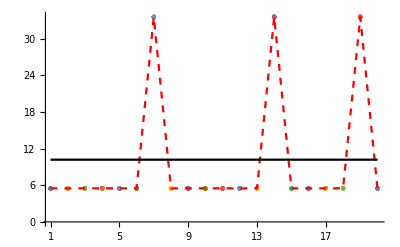

```mathematica
Which[NumericQ[forward[[1]]], 
Show[ListPlot[spot, Joined->True, PlotRange->Full], ListPlot[forward, PlotStyle-> Red], ListPlot[strike & /@ forward, PlotStyle-> Black]]
, Head[forward[[1]]]==ad, 
Show[ListPlot[MapThread[Thread[{#1, #2}]& , {Range[nE], Transpose[spot[[All, All, 1]]]}], Ticks->{Range[nE], Automatic}, PlotRange->Full], ListPlot[N[forward][[All, 1]], PlotStyle-> Directive[Red, Dashed],Joined->True, Ticks->{Range[nE], Automatic}], ListPlot[Transpose[{Range[nE],strike & /@ forward}], PlotStyle-> Black, Joined->True, Ticks->{Range[nE], Automatic}]]
,True, "Check fc !"]
```

```mathematica
Max[Exp[-exerciseDates ir](Max[#-strike, 0] & /@ forward[[All, 1]])]
```

23.389

LS

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3783,<|vol1→3.97710810338799×10^-23731,fc1→4.25802076295543×10^-23733,vol2→-1.1110509965764×10^-23714,fc2→5.5015696213438×10^-23717,vol3→-6.39804953242749×10^-23742,fc3→-5.48992659301822×10^-23745,vol4→-7.94068959583567×10^-23720,fc4→-3.0507362615564×10^-23722,vol5→-7.62065153972229×10^-23694,fc5→-1.78159547390746×10^-23696,vol6→-1.25493485237121×10^-23715,fc6→1.3981226804159×10^-23718,vol7→-2.5958821029272×10^-525,fc7→-6.83065010250599×10^-526,vol8→1.73492270054506×10^-23751,fc8→1.45500035625526×10^-23753,vol9→5.47932481029236×10^-23744,fc9→-2.23639538410164×10^-23747,vol10→1.14982952350132×10^-23760,fc10→7.43049996202034×10^-23764,vol11→2.8113491477991×10^-23762,fc11→4.89359271735006×10^-23765,vol12→3.64175001806537×10^-23763,fc12→2.51791692928633×10^-23766,vol13→-1.27890500065522×10^-23767,fc13→-1.09184930649659×10^-23770,vol14→1.11201,fc14→0.49561,vol15→1.05333486914978×10^-23709,fc15→-2.45986450352283×10^-23712,vol16→3.81427216427491×10^-23757,fc16→-1.28210713862218×10^-23759,vol17→-2.47223706745977×10^-23771,fc17→4.16527358309131×10^-23773,vol18→-4.09855119106082×10^-23755,fc18→-1.16493024272569×10^-23758,vol19→0.104666,fc19→0.503512,vol20→0.,fc20→0.|>]

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3924,<|vol1→0,fc1→0,vol2→0.,fc2→0.,vol3→0.,fc3→0.,vol4→0.,fc4→0.,vol5→0.,fc5→0.,vol6→0.,fc6→0.,vol8→0.,fc8→0.,vol9→0.,fc9→0.,vol10→0.,fc10→0.,vol11→0.,fc11→0.,vol12→0.,fc12→0.,vol13→0.,fc13→0.,vol15→0.,fc15→0.,vol16→0.,fc16→0.,vol17→0.,fc17→0.,vol18→0.,fc18→0.,vol20→0.,fc20→0.,vol19→0.0863416,fc19→0.1748,vol14→0.47975,fc14→0.0999771,vol7→0.807372,fc7→0.724816|>]

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[23.3875,<|vol1→-3.73283445436365×10^-23755,fc1→-2.23280028296385×10^-23757,vol2→5.95018480251504×10^-23757,fc2→3.2071718712007×10^-23759,vol3→9.12544882446305×10^-23760,fc3→8.00252496762464×10^-23763,vol4→6.92685413759762×10^-23762,fc4→-1.47794294486298×10^-23764,vol5→-7.0025546644164×10^-23753,fc5→-5.32882143005644×10^-23755,vol6→-1.69326289059481×10^-23758,fc6→-3.09359966395385×10^-23761,vol7→0.677813,fc7→0.567004,vol8→2.99434348851702×10^-23755,fc8→8.81514791632059×10^-23758,vol9→-3.28492413357603×10^-23765,fc9→2.15548850155581×10^-23766,vol10→9.34274311202307×10^-23770,fc10→1.27847448734045×10^-23770,vol11→-4.43784511222072×10^-23776,fc11→-1.72179804355511×10^-23779,vol12→3.59530034535991×10^-23763,fc12→1.68917091058088×10^-23766,vol13→4.14291955940206×10^-23778,fc13→7.65498809678789×10^-23782,vol14→0.901685,fc14→0.261085,vol15→-2.01059645244703×10^-23770,fc15→1.32575923384318×10^-23773,vol16→9.67318811884508×10^-23764,fc16→1.0951799218265×10^-23766,vol17→-3.78417558124342×10^-23776,fc17→-2.66587015275978×10^-23778,vol18→-5.30043345028409×10^-23727,fc18→4.14657489185665×10^-23730,vol19→-0.0661695,fc19→0.17145,vol20→0.,fc20→0.|>]

Simple

```mathematica
seqsum[vs[[1]]] / Length[vs[[1]]]
```

ad[22.5883,<|vol1→-0.000272944,fc1→-5.18553×10^-6,vol2→0.000105701,fc2→-6.78415×10^-7,vol3→-0.000015035,fc3→-1.52714×10^-7,vol4→-4.24248×10^-6,fc4→-1.41247×10^-7,vol5→-5.55529×10^-7,fc5→3.18502×10^-8,vol6→-7.39544×10^-7,fc6→-2.51478×10^-8,vol7→1.12935×10^-6,fc7→3.83679×10^-9,vol8→-7.22141×10^-8,fc8→-1.0404×10^-9,vol9→0.0510642,fc9→-0.00937263,vol10→-0.303719,fc10→0.00347498,vol11→0.0688639,fc11→0.0161802,vol12→0.0649962,fc12→0.00643082,vol13→1.65127×10^-8,fc13→-8.1758×10^-11,vol14→3.87315×10^-8,fc14→2.54247×10^-9,vol15→-1.36636×10^-8,fc15→-1.85138×10^-9,vol16→-1.54414×10^-8,fc16→2.50031×10^-10,vol17→3.7633×10^-9,fc17→1.87082×10^-10,vol18→-3.61428×10^-8,fc18→-9.76268×10^-10,vol19→0.104696,fc19→0.0342817,vol20→-0.445762,fc20→0.00403802|>]

LS

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 4.25802076295543×10^-23733 | 0. | 3.97710810338799×10^-23731 | 0.
2 | 5.5015696213438×10^-23717 | 0. | -1.1110509965764×10^-23714 | 0.
3 | -5.48992659301822×10^-23745 | 0. | -6.39804953242749×10^-23742 | 0.
4 | -3.0507362615564×10^-23722 | 0. | -7.94068959583567×10^-23720 | 0.
5 | -1.78159547390746×10^-23696 | 0. | -7.62065153972229×10^-23694 | 0.
6 | 1.3981226804159×10^-23718 | 0. | -1.25493485237121×10^-23715 | 0.
7 | -6.83065010250599×10^-526 | 0. | -2.5958821029272×10^-525 | 0.
8 | 1.45500035625526×10^-23753 | 0. | 1.73492270054506×10^-23751 | 0.
9 | -2.23639538410164×10^-23747 | 0. | 5.47932481029236×10^-23744 | 0.
10 | 7.43049996202034×10^-23764 | 0. | 1.14982952350132×10^-23760 | 0.
11 | 4.89359271735006×10^-23765 | 0. | 2.8113491477991×10^-23762 | 0.
12 | 2.51791692928633×10^-23766 | 0. | 3.64175001806537×10^-23763 | 0.
13 | -1.09184930649659×10^-23770 | 0. | -1.27890500065522×10^-23767 | 0.
14 | 0.49561 | 0.499403 | 1.11201 | 0.363134
15 | -2.45986450352283×10^-23712 | 0. | 1.05333486914978×10^-23709 | 0.
16 | -1.28210713862218×10^-23759 | 0. | 3.81427216427491×10^-23757 | 0.
17 | 4.16527358309131×10^-23773 | 0. | -2.47223706745977×10^-23771 | 0.
18 | -1.16493024272569×10^-23758 | 0. | -4.09855119106082×10^-23755 | 0.
19 | 0.503512 | 0.499635 | 0.104666 | 0.216261
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -5.4274052493569×10^-237555 | 0. | -5.256195619327×10^-237553 | 0.
2 | 2.71603986611136×10^-237422 | 0. | -6.73653770533679×10^-237420 | 0.
3 | -4.83706703110075×10^-237614 | 0. | -7.35990951975728×10^-237611 | 0.
4 | -7.58213051012076×10^-237418 | 0. | -6.27659671792355×10^-237415 | 0.
5 | -4.56520217250309×10^-237300 | 0. | -3.04827191883303×10^-237297 | 0.
6 | 7.97303705523596×10^-237460 | 0. | -6.40376898138697×10^-237457 | 0.
7 | 0.663505 | 0.577583 | 0.845256 | 0.303763
8 | 2.95958645456065×10^-237562 | 0. | 2.56082786824763×10^-237560 | 0.
9 | -3.66004672303036×10^-237584 | 0. | 1.89200691538697×10^-237580 | 0.
10 | 1.73010120760707×10^-237650 | 0. | 5.225484640225×10^-237647 | 0.
11 | 2.32944399883744×10^-237658 | 0. | 1.73164372361056×10^-237655 | 0.
12 | 2.18298828419514×10^-237647 | 0. | 2.05300679535724×10^-237644 | 0.
13 | 1.4114240393551×10^-237628 | 0. | 3.9042377710925×10^-237625 | 0.
14 | 0.142591 | 0.197573 | 0.713608 | 0.555466
15 | -4.51641456630404×10^-237078 | 0. | 1.93396706990128×10^-237075 | 0.
16 | -9.17322142159098×10^-237557 | 0. | 2.71811895314064×10^-237554 | 0.
17 | 2.77983631048129×10^-237698 | 0. | -1.48443891470433×10^-237696 | 0.
18 | -2.80648334473347×10^-237526 | 0. | -7.98256542319315×10^-237523 | 0.
19 | 0.193472 | 0.224279 | -0.113659 | -0.0289138
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -2.49255438036029×10^-237479 | 0. | -8.75817294407484×10^-237476 | 0.
2 | 4.58380913483279×10^-237484 | 0. | 1.38057771155252×10^-237482 | 0.
3 | -2.19163478547698×10^-237642 | 0. | 1.29008666397279×10^-237640 | 0.
4 | 3.82509529827915×10^-237601 | 0. | -2.86279956942715×10^-237598 | 0.
5 | -1.34270775768941×10^-237348 | 0. | 1.27017100184539×10^-237344 | 0.
6 | -3.27169018971721×10^-237730 | 0. | -9.18225507175832×10^-237728 | 0.
7 | 0.587176 | 0.551926 | 1.6784 | 1.02876
8 | -7.52441291831715×10^-237705 | 0. | 3.66477031228861×10^-237702 | 0.
9 | 4.60853999628934×10^-237704 | 0. | -6.94535192333214×10^-237701 | 0.
10 | -4.33303627205417×10^-237790 | 0. | -8.12815237423811×10^-237788 | 0.
11 | 2.27403110126384×10^-237753 | 0. | -2.18267823455118×10^-237751 | 0.
12 | 3.67344976788068×10^-237809 | 0. | 2.92796148188805×10^-237806 | 0.
13 | -1.05814661166837×10^-237766 | 0. | -9.82929486101079×10^-237764 | 0.
14 | 0.279336 | 0.279207 | 0.968931 | 0.898799
15 | 2.05325862584566×10^-237384 | 0. | 2.03168043401288×10^-237381 | 0.
16 | -3.22048823997539×10^-237366 | 0. | -3.53719497385504×10^-237363 | 0.
17 | 5.6392298030645×10^-237678 | 0. | 2.45482748736571×10^-237675 | 0.
18 | 5.7836653716537×10^-237398 | 0. | 3.2288723143041×10^-237395 | 0.
19 | 0.13318 | 0.168439 | -0.161161 | -0.128084
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 6.6881400720423×10^-237643 | 0. | 1.1018752438468×10^-237640 | 0.
2 | 1.71138063638962×10^-237595 | 0. | 3.14223259382026×10^-237593 | 0.
3 | 1.76928332997489×10^-237676 | 0. | 1.88561688486753×10^-237673 | 0.
4 | -5.03094703358281×10^-237645 | 0. | 1.96391599779536×10^-237642 | 0.
5 | -8.3366715595266×10^-237461 | 0. | -1.03072498142147×10^-237458 | 0.
6 | -6.50606416077727×10^-237638 | 0. | -4.25832147402225×10^-237635 | 0.
7 | 0.556637 | 0.52825 | 1.57472 | 0.925786
8 | 2.1729440128927×10^-237572 | 0. | 7.05475393416936×10^-237570 | 0.
9 | 3.88566779789639×10^-237722 | 0. | -4.97037695548022×10^-237721 | 0.
10 | 1.42545800707801×10^-237796 | 0. | 1.87104708870919×10^-237796 | 0.
11 | 4.83315218909113×10^-237817 | 0. | 2.23684924625657×10^-237814 | 0.
12 | 3.61760831676207×10^-237740 | 0. | 8.15280859578532×10^-237737 | 0.
13 | 1.03798608213576×10^-237873 | 0. | 5.54832882725053×10^-237870 | 0.
14 | 0.310752 | 0.29279 | 1.34628 | 1.16934
15 | 4.42283015206491×10^-237688 | 0. | -5.38423424146026×10^-237685 | 0.
16 | -8.56337345667078×10^-237596 | 0. | -7.70500408190424×10^-237593 | 0.
17 | -1.13507241576207×10^-237737 | 0. | -1.59315051212782×10^-237735 | 0.
18 | 7.35134695407992×10^-237240 | 0. | -9.3969906046005×10^-237237 | 0.
19 | 0.132313 | 0.178532 | -0.254851 | -0.187108
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -1.64107103215699×10^-118811 | 0. | -2.8946453515351×10^-118809 | 0.
2 | 4.30085451851616×10^-118795 | 0. | 8.31991820636702×10^-118793 | 0.
3 | 3.43046198306886×10^-118828 | 0. | 3.77471607583637×10^-118825 | 0.
4 | -5.27667053716515×10^-118817 | 0. | 2.18382348344775×10^-118814 | 0.
5 | -2.45035579445484×10^-118741 | 0. | -3.12309368915709×10^-118739 | 0.
6 | -5.5092689976191×10^-118805 | 0. | -3.42504078338798×10^-118802 | 0.
7 | 0.566256 | 0.534108 | 1.3615 | 0.69079
8 | 1.98691582427737×10^-118781 | 0. | 6.46682624673776×10^-118779 | 0.
9 | 1.08226774012856×10^-118850 | 0. | -1.43464503929738×10^-118849 | 0.
10 | 5.15808751490936×10^-118885 | 0. | 9.81031111404628×10^-118885 | 0.
11 | 1.94280403812081×10^-118901 | 0. | 7.79589250457644×10^-118899 | 0.
12 | 2.55077405401992×10^-118848 | 0. | 5.77230900808142×10^-118845 | 0.
13 | 5.25070877249206×10^-118924 | 0. | 2.77938696422228×10^-118920 | 0.
14 | 0.292617 | 0.280244 | 1.27392 | 0.993785
15 | 1.3988997105502×10^-118846 | 0. | -1.72670447091896×10^-118843 | 0.
16 | -8.89943459442655×10^-118802 | 0. | -8.01138080133443×10^-118799 | 0.
17 | -2.60786645090491×10^-118871 | 0. | -3.67084637981202×10^-118869 | 0.
18 | 3.12141238379129×10^-118623 | 0. | -3.99000115581424×10^-118620 | 0.
19 | 0.140801 | 0.185175 | -0.188429 | -0.120627
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | -2.23280028296385×10^-23757 | 0. | -3.73283445436365×10^-23755 | 0.
2 | 3.2071718712007×10^-23759 | 0. | 5.95018480251504×10^-23757 | 0.
3 | 8.00252496762464×10^-23763 | 0. | 9.12544882446305×10^-23760 | 0.
4 | -1.47794294486298×10^-23764 | 0. | 6.92685413759762×10^-23762 | 0.
5 | -5.32882143005644×10^-23755 | 0. | -7.0025546644164×10^-23753 | 0.
6 | -3.09359966395385×10^-23761 | 0. | -1.69326289059481×10^-23758 | 0.
7 | 0.567004 | 0.534172 | 0.677813 | 0.220685
8 | 8.81514791632059×10^-23758 | 0. | 2.99434348851702×10^-23755 | 0.
9 | 2.15548850155581×10^-23766 | 0. | -3.28492413357603×10^-23765 | 0.
10 | 1.27847448734045×10^-23770 | 0. | 9.34274311202307×10^-23770 | 0.
11 | -1.72179804355511×10^-23779 | 0. | -4.43784511222072×10^-23776 | 0.
12 | 1.68917091058088×10^-23766 | 0. | 3.59530034535991×10^-23763 | 0.
13 | 7.65498809678789×10^-23782 | 0. | 4.14291955940206×10^-23778 | 0.
14 | 0.261085 | 0.25806 | 0.901685 | 0.608542
15 | 1.32575923384318×10^-23773 | 0. | -2.01059645244703×10^-23770 | 0.
16 | 1.0951799218265×10^-23766 | 0. | 9.67318811884508×10^-23764 | 0.
17 | -2.66587015275978×10^-23778 | 0. | -3.78417558124342×10^-23776 | 0.
18 | 4.14657489185665×10^-23730 | 0. | -5.30043345028409×10^-23727 | 0.
19 | 0.17145 | 0.207185 | -0.0661695 | -0.0223701
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 0 | 0. | 0 | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0. | 0. | 0. | 0.
6 | 0. | 0. | 0. | 0.
7 | 0.724816 | 0.724816 | 0.807372 | 0.807372
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0.0999771 | 0.0999771 | 0.47975 | 0.47975
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0. | 0. | 0. | 0.
18 | 0. | 0. | 0. | 0.
19 | 0.1748 | 0.1748 | 0.0863416 | 0.0863416
20 | 0. | 0. | 0. | 0.

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]],fc,vol},
fc="fc"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
vol="vol"<>ToString[#] & /@ Range[Length[res[[2]]]/2];
TableForm[Transpose[{Range[Length[fc]], res[[2]][#] & /@ fc, fcbar[[All,1]],res[[2]][#] & /@ vol, volbar[[All,1]]}], TableHeadings->{None, {"day","delta_ad", "delta_manual", "vega_ad", "vega_manual" }}]
]
```

day | delta_ad | delta_manual | vega_ad | vega_manual
1 | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0.
4 | 0. | 0. | 0. | 0.
5 | 0. | 0. | 0. | 0.
6 | 0. | 0. | 0. | 0.
7 | 0.724816 | 0.724816 | 0.807372 | 0.807372
8 | 0. | 0. | 0. | 0.
9 | 0. | 0. | 0. | 0.
10 | 0. | 0. | 0. | 0.
11 | 0. | 0. | 0. | 0.
12 | 0. | 0. | 0. | 0.
13 | 0. | 0. | 0. | 0.
14 | 0.0999771 | 0.0999771 | 0.47975 | 0.47975
15 | 0. | 0. | 0. | 0.
16 | 0. | 0. | 0. | 0.
17 | 0. | 0. | 0. | 0.
18 | 0. | 0. | 0. | 0.
19 | 0.1748 | 0.1748 | 0.0863416 | 0.0863416
20 | 0. | 0. | 0. | 0.

1k sims

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]]},
TableForm[Transpose[{Range[Length[vs]], fcbar,volbar}], TableHeadings->{None, {"day","delta_manual", "vega_manual" }}]
]
```

day | delta_manual | vega_manual
1 | 0. | 0.
2 | 0. | 0.
3 | 0.0130472 | 0.000897061
4 | 0.169472 | 0.00729841
5 | 0.289231 | 0.00738155
6 | 0.17273 | 0.00301251
7 | 0.0581684 | 0.000698378
8 | 0.00690373 | -0.000119574
9 | 0.000696961 | 0.0000494829
10 | 0. | 0.
11 | 0. | 0.
12 | 0. | 0.
13 | 0. | 0.
14 | 0. | 0.
15 | 0. | 0.
16 | 0. | 0.
17 | 0. | 0.
18 | 0. | 0.
19 | 0. | 0.
20 | 0. | 0.

10k sims

```mathematica
Module[{res=seqsum[vs[[1]]] / Length[vs[[1]]]},
TableForm[Transpose[{Range[Length[vs]], fcbar,volbar}], TableHeadings->{None, {"day","delta_manual", "vega_manual" }}]
]
```

day | delta_manual | vega_manual
1 | 0. | 0.
2 | 0. | 0.
3 | 0.0134607 | 0.000907438
4 | 0.170779 | 0.00741076
5 | 0.281584 | 0.00781044
6 | 0.187397 | 0.00341653
7 | 0.0518907 | 0.000583088
8 | 0.00658878 | 0.0000506197
9 | 0.000807085 | 0.0000101221
10 | 0.0000590161 | 2.66501×10^-6
11 | 0. | 0.
12 | 0. | 0.
13 | 0. | 0.
14 | 0. | 0.
15 | 0. | 0.
16 | 0. | 0.
17 | 0. | 0.
18 | 0. | 0.
19 | 0. | 0.
20 | 0.0000428829 | -1.96197×10^-6

Simple

### mod_payoff